NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{{n→InterpolatingFunction[…]}}

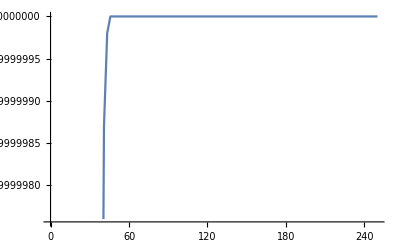

```mathematica
Clear["Global`*"]
a=20;
k=100;
r=0.1;
nzero=50;
T=0.8;
s=NDSolve[{n'[t]==r*n[t] (1-n[t-T]/k) (n[t]/a-1),n[0]==nzero},n,{t,0,200}]
Plot[s[[1,1,2]][t], {t,0,200}]
```